# Old case -- fully symmetric rings

## Coupled mode theory

```mathematica
H[μ_]:=({{(ω1[μ]-(d1×μ)), -J, 0}, {-J, (ω2[μ]-(d1×μ)), -J}, {0, -J, (ω3[μ]-(d1×μ))}});
```

```mathematica
ω1[μ_]:=ω0 +d1×μ + d2/2 μ^2+δ1;
ω2[μ_]:=ω0 + D1×(2μ) + D2/2(2μ)^2+δ2;
ω3[μ_]:=ω0+d1×μ + d2/2 μ^2 +δ3;
```

```mathematica
δ1=-.2;δ2= -0.168;δ3= -.252;
δ1=0;δ2= 0;δ3= 0;
```

## Dispersion

```mathematica
d1=454.66; (* FSR *)
d2=-0.01533;(*-8.08×10^-3;*) (* GVD *)
D1=454.66*0.9945/2;
D2=-0.01533;
J[μ_]:=3.43343343/(√2);(* Splitting *)
(*J[μ_]:= E^(0.02071371*μ + 1.09238286) + 0.65560241;*)
ω0=0;
```

```mathematica
J = 3.43343343/(√2);
```

## Coupled modes in function of μ

```mathematica
sortedEig[μ_]:=sortedEig[μ]=Module[{vals,vecs,pairs,fixSign},(*flip sign if the first component is negative*)
fixSign[v_]:=v/Sign[v[[1]]];
(*If[Re[v[[1]]]<0,-v,v];*)
{vals,vecs}=Eigensystem[H[μ]];
vecs=fixSign/@vecs;
pairs=Transpose[{vals,vecs}];
SortBy[pairs,First]];
```

```mathematica
ωS[μ_]:=sortedEig[μ][[1,1]];  (*smallest eigenvalue*)
bS[μ_]:=Normalize[sortedEig[μ][[1,2]]];

ωC[μ_]:=sortedEig[μ][[2,1]];
bC[μ_]:=Normalize[sortedEig[μ][[2,2]]];

ωAS[μ_]:=sortedEig[μ][[3,1]];  (*largest eigenvalue*)
bAS[μ_]:=Normalize[sortedEig[μ][[3,2]]];
```

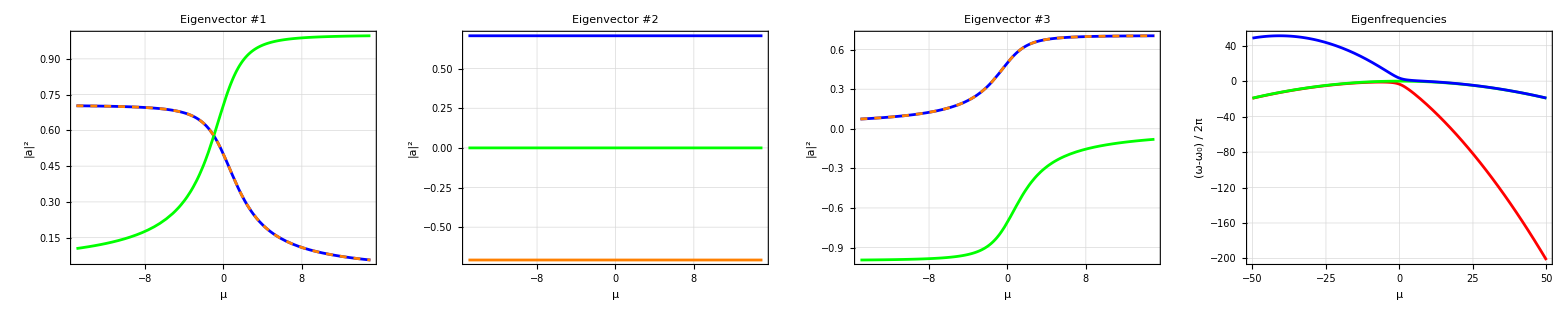

```mathematica
plt1=Plot[{bS[μ][[1]],bS[μ][[2]],bS[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #1",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Blue,Green,{Orange,Dashed}}];
plt2=Plot[{bC[μ][[1]],bC[μ][[2]],bC[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #2",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Blue,Green,Orange}];
plt3=Plot[{bAS[μ][[1]],bAS[μ][[2]],bAS[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #3",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Blue,Green,{Orange,Dashed}}];
plt4=Plot[{ωS[μ],ωC[μ],ωAS[μ]},{μ,-50,50},FrameLabel->{"μ","(ω-ω_0) / 2π"},PlotLabel->"Eigenfrequencies",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue}];
Grid[{{plt1,plt2,plt3,plt4}},ItemSize->Automatic,BaseStyle->ImageSizeMultipliers->1]
```

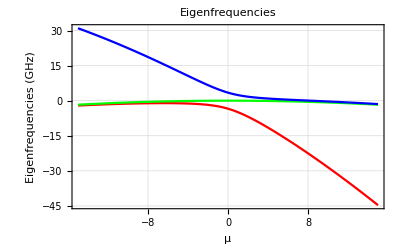

```mathematica
Plot[{ωS[μ],ωC[μ],ωAS[μ]},{μ,-15,15},FrameLabel->{"μ","Eigenfrequencies (GHz)"},PlotLabel->"Eigenfrequencies",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue}]
```

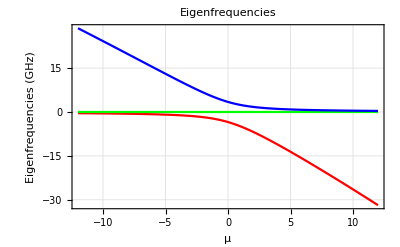

```mathematica
Plot[{ωS[μ]-ωC[μ],ωC[μ]-ωC[μ],ωAS[μ]-ωC[μ]},{μ,-12,12},FrameLabel->{"μ","Eigenfrequencies (GHz)"},PlotLabel->"Eigenfrequencies",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue}]
```

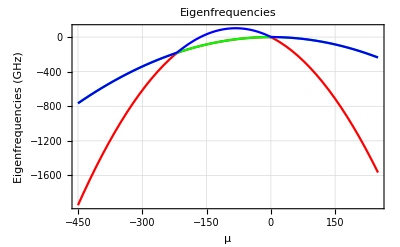

```mathematica
Plot[{ωS[μ],ωC[μ],ωAS[μ]},{μ,-450,250},FrameLabel->{"μ","Eigenfrequencies (GHz)"},PlotLabel->"Eigenfrequencies",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue}]
```

```mathematica
{ωS[100000]-ω1[100000],ωC[100000]-ω1[100000],ωAS[100000]-ω2[100000]}
```

{3.0415×10^7,3.0415×10^7,2.57712×10^8}

```mathematica
{bS[10000],bC[10000],bAS[10000]}//MatrixForm
```

(0.707107 | 2.96279×10^-6 | 0.707107
0.707107 | -7.40104×10^-21 | -0.707107
2.09501×10^-6 | -1. | 2.09501×10^-6)

## Overlapping

#### Overlap with central supermode

```mathematica
a1={1,0,0};
```

```mathematica
ΓS[μ_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bS[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]]^2,{i,1,3}]
ΓC[μ_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bC[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]]^2,{i,1,3}]
ΓAS[μ_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bAS[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]]^2,{i,1,3}]
Γa1[μ_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[a1[[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]]^2,{i,1,3}]
```

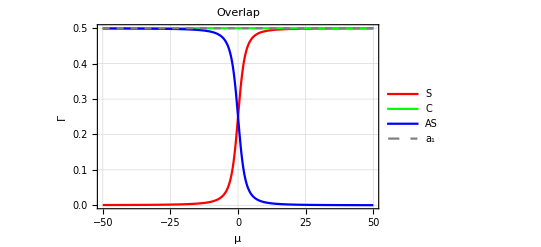

```mathematica
Plot[{ΓS[μ],ΓC[μ],ΓAS[μ], Γa1[μ]},{μ,-50,50},FrameLabel->{"μ","Γ"},PlotLabel->"Overlap",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue,{Gray,Dashed}},PlotLegends->{"S", "C", "AS", "a_1"}]
```

Self-overlap of C mode is equal to its overlap with the first ring:

```mathematica
j=1;
Abs[1/(1+KroneckerDelta[2,j])Conjugate[a1[[j]]]*1/(1+KroneckerDelta[2,j])bC[0][[j]]]^2
Abs[1/(1+KroneckerDelta[2,j])Conjugate[bC[0][[j]]]*1/(1+KroneckerDelta[2,j])bC[0][[j]]]^2
```

0.5

0.25

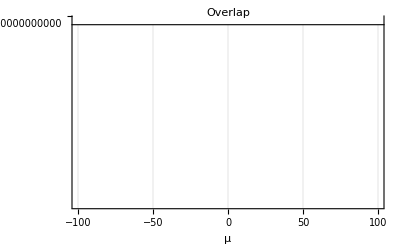

```mathematica
Plot[{ΓC[μ], Γa1[μ]},{μ,-100,100},FrameLabel->{"μ","Γ"},PlotLabel->"Overlap",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Green,{Orange,Dashed}}]
```

#### Overlap for OPO

```mathematica
ΛS[μ_]:=Sum[1/(1+KroneckerDelta[2,i])Conjugate[bS[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]*1/(1+KroneckerDelta[2,i])Conjugate[bAS[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]],{i,1,3}];
ΛC[μ_]:=Sum[1/(1+KroneckerDelta[2,i])Conjugate[bC[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]*1/(1+KroneckerDelta[2,i])Conjugate[bC[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]],{i,1,3}];
ΛAS[μ_]:=Sum[1/(1+KroneckerDelta[2,i])Conjugate[bAS[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]*1/(1+KroneckerDelta[2,i])Conjugate[bS[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]],{i,1,3}];
ΛSG[μ_]:=Sum[1/(1+KroneckerDelta[2,i])Conjugate[a1[[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]*1/(1+KroneckerDelta[2,i])Conjugate[a1[[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]],{i,1,3}];
```

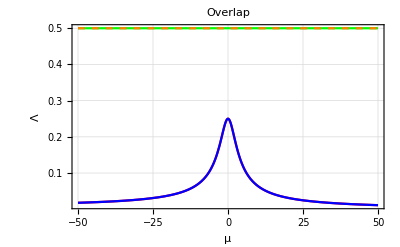

```mathematica
Plot[{ΛS[μ],ΛC[μ],ΛAS[μ],ΛSG[μ]},{μ,-50,50},FrameLabel->{"μ","Λ"},PlotLabel->"Overlap",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue,{Orange,Dashed}}]
```

## Losses

```mathematica
S[μ_]:=({{bS[μ][[1]], bC[μ][[1]], bAS[μ][[1]]}, {bS[μ][[2]], bC[μ][[2]], bAS[μ][[2]]}, {bS[μ][[3]], bC[μ][[3]], bAS[μ][[3]]}}); (*Similarity matrix*)
```

```mathematica
Γ=({{(κi+κe)/2, 0, 0}, {0, κi, 0}, {0, 0, (κi+κe)/2}}); (*Losses in the uncoupled basis*)
```

```mathematica
Γb[μ_]:=Inverse[S[μ]].Γ.S[μ] (*Losses in the coupled basis*)
```

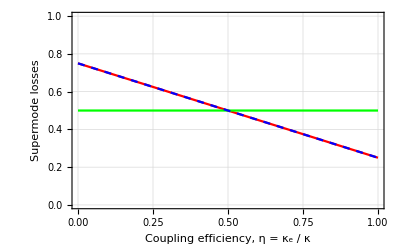

```mathematica
rcoupling={κe->η ,κi->1-η};
Plot[{Γb[0][[1,1]],Γb[0][[2,2]],Γb[0][[3,3]]}/.rcoupling//Evaluate,{η,0,1},PlotRange->{Full,{0,1}},FrameLabel->{"Coupling efficiency, η = κ_e / κ","Supermode losses"},Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,{Blue,Dashed}}]
```

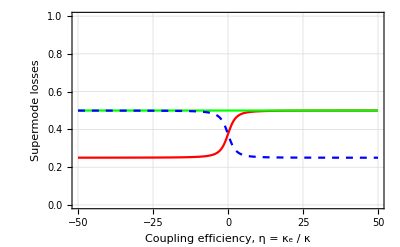

```mathematica
rcoupling={κi->.25 ,κe->.75};
Plot[{Γb[μ][[1,1]],Γb[μ][[2,2]],Γb[μ][[3,3]]}/.rcoupling//Evaluate,{μ,-50,50},PlotRange->{Full,{0,1}},FrameLabel->{"Coupling efficiency, η = κ_e / κ","Supermode losses"},Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,{Blue,Dashed}}]
```

```mathematica
μtest=100;
{Γb[μtest][[1,1]],Γb[μtest][[2,2]],Γb[μtest][[3,3]]}/.rcoupling
```

{0.499955+0.0094855 (0.+0.0094855 (1-η)),0.5+2.02098×10^-18 (0.+5.51961×10^-18 (1-η)),0.0000449874-0.999955 (0.-0.999955 (1-η))}

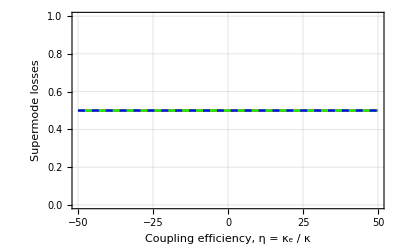

```mathematica
rcoupling={κe->.5 ,κi->.5};
Plot[{Γb[μ][[1,1]],Γb[μ][[2,2]],Γb[μ][[3,3]]}/.rcoupling//Evaluate,{μ,-50,50},PlotRange->{Full,{0,1}},FrameLabel->{"Coupling efficiency, η = κ_e / κ","Supermode losses"},Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,{Blue,Dashed}}]
```

## Parametric gain

```mathematica
GMatrixC[μ_]:= ({{-κ/2+I( 2ΓC[μ]Pp -ωC[μ]), I ΛC[μ] Pp}, {- I  ΛC[-μ]Pp, -κ/2-I( 2ΓC[-μ]Pp -ωC[-μ])}});
λC[μ_]:=Eigenvalues[GMatrixC[μ]]//MatrixForm;
gC[μ_]:=Re[λC[μ][[1,2]]];
GMatrixS[μ_]:= ({{-κ/2+I( 2ΓS[μ]Pp -ωS[μ]), I ΛS[μ] Pp}, {- I  ΛAS[-μ]Pp, -κ/2-I( 2ΓAS[-μ]Pp -ωAS[-μ])}});
λS[μ_]:=Eigenvalues[GMatrixS[μ]]//MatrixForm;
gS[μ_]:=Re[λS[μ][[1,2]]];
GMatrixAS[μ_]:= ({{-κ/2+I( 2ΓAS[μ]Pp -ωAS[μ]), I ΛAS[μ] Pp}, {- I  ΛS[-μ]Pp, -κ/2-I( 2ΓS[-μ]Pp -ωS[-μ])}});
λAS[μ_]:=Eigenvalues[GMatrixAS[μ]]//MatrixForm;
gAS[μ_]:=Re[λAS[μ][[1,2]]];
GMatrixSG[μ_]:= ({{-κ/2+I( 2Pp -d2/2 μ^2), I  Pp}, {- I  Pp, -κ/2-I( 2Pp  -d2/2 μ^2)}});
λSG[μ_]:=Eigenvalues[GMatrixSG[μ]]//MatrixForm;
gSG[μ_]:=Re[λSG[μ][[1,2]]];
```

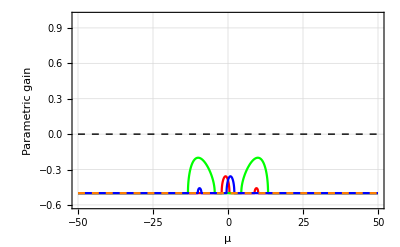

```mathematica
rplot = {κ->1,Pp->.3};
Plot[{gS[μ]/.rplot,gC[μ]/.rplot,gAS[μ]/.rplot,gSG[μ]/.rplot},{μ,-50,50},PlotRange->{Full,{-.6,1}},FrameLabel->{"μ","Parametric gain"},Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue,{Orange,Dashed}},Epilog->{Directive[Black,Dashed],Line[{{-50,0},{50,0}}]}]
```

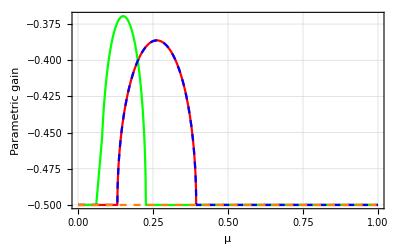

```mathematica
rplot = {κ->1,Pp->Pplot};
Plot[{gS[0]/.rplot,gC[0]/.rplot,gAS[0]/.rplot,gSG[0]/.rplot},{Pplot,0,1},PlotRange->Full,FrameLabel->{"μ","Parametric gain"},Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,{Blue,Dashed},{Orange,Dashed}}]
```

# Main (750 600)

## Parametric gain -- Assymetric rings

```mathematica
ClearAll["Global`*"]
```

#### Definitions

```mathematica
H[μ_,δ1_,δ2_,δ3_]:=({{(ω1[μ,δ1]-d1×μ), -J[μ], 0}, {-J[μ], (ω2[μ,δ2]-d1×μ), -J[μ]}, {0, -J[μ], (ω3[μ,δ3]-d1×μ)}});
```

```mathematica
ω1[μ_,δ1_]:=ω0 +d1×μ + d2/2 μ^2+δ1;
ω2[μ_,δ2_]:=ω0 + D1×(2μ) + D2/2(2μ)^2+δ2;
ω3[μ_,δ3_]:=ω0+d1×μ + d2/2 μ^2 +δ3;
```

```mathematica
d1=454.66; (* FSR *)
d2=-0.01533;(*-8.08×10^-3;*) (* GVD *)
D1=454.66*0.9945/2;
D2=-0.01533;
J[μ_]:=3.43343343/(√2);(* Splitting *)
(*J[μ_]:= E^(0.02071371*μ + 1.09238286) + 0.65560241;*)
ω0=0;
```

#### Eigenproblem

```mathematica
sortedEig[μ_,δ1_,δ2_,δ3_]:=sortedEig[μ,δ1,δ2,δ3]=Module[{vals,vecs,pairs,fixSign},
fixSign[v_]:=If[Re[v[[1]]]<0,-v,v];
{vals,vecs}=Eigensystem[H[μ,δ1,δ2,δ3]];
vecs=fixSign/@vecs;
pairs=Transpose[{vals,vecs}];
SortBy[pairs,First]];
```

```mathematica
ωS[μ_,δ1_,δ2_,δ3_]:=sortedEig[μ,δ1,δ2,δ3][[1,1]];  (*smallest eigenvalue*)
bS[μ_,δ1_,δ2_,δ3_]:=Normalize[sortedEig[μ,δ1,δ2,δ3][[1,2]]];

ωC[μ_,δ1_,δ2_,δ3_]:=sortedEig[μ,δ1,δ2,δ3][[2,1]];
bC[μ_,δ1_,δ2_,δ3_]:=Normalize[sortedEig[μ,δ1,δ2,δ3][[2,2]]];

ωAS[μ_,δ1_,δ2_,δ3_]:=sortedEig[μ,δ1,δ2,δ3][[3,1]];  (*largest eigenvalue*)
bAS[μ_,δ1_,δ2_,δ3_]:=Normalize[sortedEig[μ,δ1,δ2,δ3][[3,2]]];
```

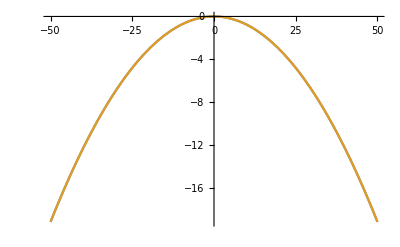

```mathematica
Plot[{ωC[μ,0,0,0],ω1[μ,0]-d1×μ},{μ,-50,50}]
```

#### Overlap integrals (XPM and OPO)

```mathematica
ΓS[μ_,δ1_,δ2_,δ3_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bS[μ,δ1,δ2,δ3][[i]]]*1/(1+KroneckerDelta[2,i])bC[0,δ1,δ2,δ3][[i]]]^2,{i,1,3}]
ΓC[μ_,δ1_,δ2_,δ3_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bC[μ,δ1,δ2,δ3][[i]]]*1/(1+KroneckerDelta[2,i])bC[0,δ1,δ2,δ3][[i]]]^2,{i,1,3}]
ΓAS[μ_,δ1_,δ2_,δ3_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bAS[μ,δ1,δ2,δ3][[i]]]*1/(1+KroneckerDelta[2,i])bC[0,δ1,δ2,δ3][[i]]]^2,{i,1,3}]
```

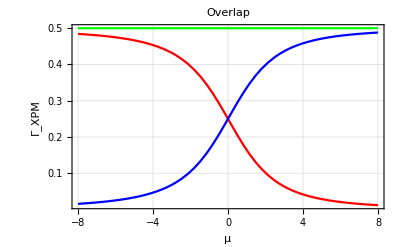

```mathematica
Plot[{ΓS[μ,0,0,0],ΓC[μ,0,0,0],ΓAS[μ,0,0,0]},{μ,-8,8},FrameLabel->{"μ","Γ_XPM"},PlotLabel->"Overlap",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue, {Orange,Dashed}}]
```

```mathematica
ΛS[μ_,δ1_,δ2_,δ3_]:=Sum[1/(1+KroneckerDelta[2,i])Conjugate[bS[μ,δ1,δ2,δ3][[i]]]*1/(1+KroneckerDelta[2,i])bC[0,δ1,δ2,δ3][[i]]*1/(1+KroneckerDelta[2,i])Conjugate[bAS[μ,δ1,δ2,δ3][[i]]]*1/(1+KroneckerDelta[2,i])bC[0,δ1,δ2,δ3][[i]],{i,1,3}];
ΛC[μ_,δ1_,δ2_,δ3_]:=Sum[1/(1+KroneckerDelta[2,i])Conjugate[bC[μ,δ1,δ2,δ3][[i]]]*1/(1+KroneckerDelta[2,i])bC[0,δ1,δ2,δ3][[i]]*1/(1+KroneckerDelta[2,i])Conjugate[bC[μ,δ1,δ2,δ3][[i]]]*1/(1+KroneckerDelta[2,i])bC[0,δ1,δ2,δ3][[i]],{i,1,3}];
ΛAS[μ_,δ1_,δ2_,δ3_]:=Sum[1/(1+KroneckerDelta[2,i])Conjugate[bAS[μ,δ1,δ2,δ3][[i]]]*1/(1+KroneckerDelta[2,i])bC[0,δ1,δ2,δ3][[i]]*1/(1+KroneckerDelta[2,i])Conjugate[bS[μ,δ1,δ2,δ3][[i]]]*1/(1+KroneckerDelta[2,i])bC[0,δ1,δ2,δ3][[i]],{i,1,3}];
```

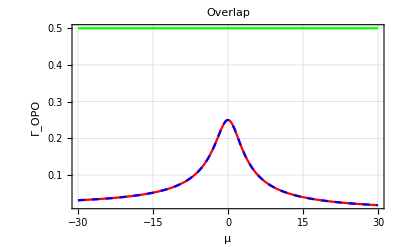

```mathematica
Plot[{ΛS[μ,0,0,0],ΛC[μ,0,0,0],ΛAS[μ,0,0,0]},{μ,-30,30},FrameLabel->{"μ","Γ_OPO"},PlotLabel->"Overlap",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,{Blue,Dashed}}]
```

Export

```mathematica
muVals=Range[-50,50,0.1];
```

```mathematica
data=Table[{mu,ΛS[mu,0,0,0],ΛC[mu,0,0,0],ΛAS[mu,0,0,0]},{mu,muVals}];
```

General::munfl: (3.81982×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(3.81982×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
dataWithHeader=Prepend[data,{"mu","S","C","AS"}];
```

```mathematica
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\uploads\\Luca\\Mathematica\\OPO in oOo\\oOo_asymmetric_overlaps.csv",dataWithHeader]
```

G:\.shortcut-targets-by-id\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\LPD Team\uploads\Luca\Mathematica\OPO in oOo\oOo_asymmetric_overlaps.csv

#### Frequency mismatch

```mathematica
ΔνS[μ_]:= (ωS[μ,0,0,0]-ωC[0,0,0,0]) - (ωC[0,0,0,0]-ωAS[-μ,0,0,0])
ΔνC[μ_]:= (ωC[μ,0,0,0]-ωC[0,0,0,0]) - (ωC[0,0,0,0]-ωC[-μ,0,0,0]) 
ΔνAS[μ_]:= (ωAS[μ,0,0,0]-ωC[0,0,0,0]) - (ωC[0,0,0,0]-ωS[-μ,0,0,0])
```

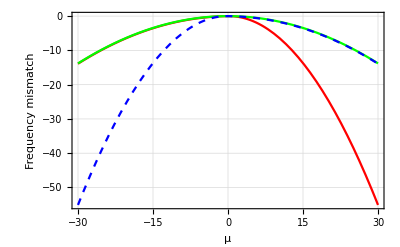

```mathematica
Plot[{ΔνS[μ],ΔνC[μ],ΔνAS[μ]},{μ,-30,30},FrameLabel->{"μ","Frequency mismatch"},PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,{Blue,Dashed}}]
```

Export

```mathematica
muVals=Range[-50,50,0.1];
```

```mathematica
data=Table[{mu,ΔνS[mu],ΔνC[mu],ΔνAS[mu]},{mu,muVals}];
```

```mathematica
dataWithHeader=Prepend[data,{"mu","S","C","AS"}];
```

```mathematica
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\uploads\\Luca\\Mathematica\\OPO in oOo\\oOo_asymmetric_mismatch.csv",dataWithHeader]
```

G:\.shortcut-targets-by-id\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\LPD Team\uploads\Luca\Mathematica\OPO in oOo\oOo_asymmetric_mismatch.csv

#### Supermodes’ losses

```mathematica
S[μ_,δ1_,δ2_,δ3_]:=({{bS[μ,δ1,δ2,δ3][[1]], bC[μ,δ1,δ2,δ3][[1]], bAS[μ,δ1,δ2,δ3][[1]]}, {bS[μ,δ1,δ2,δ3][[2]], bC[μ,δ1,δ2,δ3][[2]], bAS[μ,δ1,δ2,δ3][[2]]}, {bS[μ,δ1,δ2,δ3][[3]], bC[μ,δ1,δ2,δ3][[3]], bAS[μ,δ1,δ2,δ3][[3]]}}); (*Similarity matrix*)
```

```mathematica
Γ=({{(κi+κe)/2, 0, 0}, {0, κi, 0}, {0, 0, (κi+κe)/2}}); (*Losses in the uncoupled basis*)
```

```mathematica
Γb[μ_,δ1_,δ2_,δ3_]:=Inverse[S[μ,δ1,δ2,δ3]].Γ.S[μ,δ1,δ2,δ3] /.{κi->.75, κe->.25}(*Losses in the coupled basis*)
```

```mathematica
κS[μ_,δ1_,δ2_,δ3_]:=Γb[μ,δ1,δ2,δ3][[1,1]];
κC[μ_,δ1_,δ2_,δ3_]:=Γb[μ,δ1,δ2,δ3][[2,2]];
κAS[μ_,δ1_,δ2_,δ3_]:=Γb[μ,δ1,δ2,δ3][[3,3]];
```

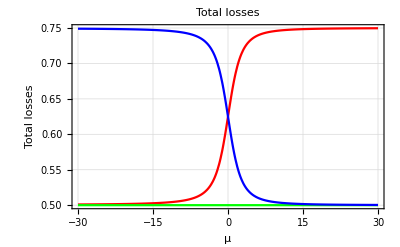

```mathematica
Plot[{κS[μ,0,0,0],κC[μ,0,0,0],κAS[μ,0,0,0]},{μ,-30,30},FrameLabel->{"μ","Total losses"},PlotLabel->"Total losses",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue}]
```

#### Parametric gain

General case

```mathematica
K=({{Mismatch[μ], G[μ]}, {- G[-μ], Mismatch[-μ]}});
λ=Eigenvalues[K]//MatrixForm
```

(1/2 (Mismatch[-μ]+Mismatch[μ]-√(-4 G[-μ] G[μ]+Mismatch[-μ]^2-2 Mismatch[-μ] Mismatch[μ]+Mismatch[μ]^2))
1/2 (Mismatch[-μ]+Mismatch[μ]+√(-4 G[-μ] G[μ]+Mismatch[-μ]^2-2 Mismatch[-μ] Mismatch[μ]+Mismatch[μ]^2)))

C supermode

```mathematica
ΔeffC[μ_,ωp_,δ1_,δ2_,δ3_]:=2ΓC[μ,δ1,δ2,δ3]Pp -(ωC[μ,δ1,δ2,δ3]-ωp)
λC[μ_,ωp_,δ1_,δ2_,δ3_]:=1/2 (MismatchC[-μ]+MismatchC[μ]+√(-4 G[-μ] G[μ]+MismatchC[-μ]^2-2 MismatchC[-μ] MismatchC[μ]+MismatchC[μ]^2))/.{MismatchC[μ]->-κC[μ,δ1,δ2,δ3]/2+I ΔeffC[μ,ωp, δ1,δ2,δ3],MismatchC[-μ]->-κC[μ,δ1,δ2,δ3]/2-I ΔeffC[-μ,-ωp,δ1,δ2,δ3],G[μ]->I  ΛC[μ,δ1,δ2,δ3] Pp,G[-μ]->I  ΛC[-μ,δ1,δ2,δ3] Pp};
gC[μ_,ωp_,Pplot_,δ1_,δ2_,δ3_]:=Re[λC[μ,ωp,δ1,δ2,δ3]]/.{Pp->Pplot};
```

S and AS supermode

```mathematica
ΔeffS[μ_,ωp_,δ1_,δ2_,δ3_]:=2ΓS[μ,δ1,δ2,δ3]Pp -(ωS[μ,δ1,δ2,δ3]-ωp)
ΔeffAS[μ_,ωp_,δ1_,δ2_,δ3_]:=2ΓAS[μ,δ1,δ2,δ3]Pp -(ωAS[μ,δ1,δ2,δ3]-ωp)
λS[μ_,ωp_,δ1_,δ2_,δ3_]:=1/2 (MismatchAS[-μ]+MismatchS[μ]+√(-4 GAS[-μ] GS[μ]+MismatchAS[-μ]^2-2 MismatchAS[-μ] MismatchS[μ]+MismatchS[μ]^2))/.{MismatchS[μ]->-κS[μ,δ1,δ2,δ3]/2+I ΔeffS[μ,ωp, δ1,δ2,δ3],MismatchAS[-μ]->-κAS[-μ,δ1,δ2,δ3]/2-I ΔeffAS[-μ,ωp,δ1,δ2,δ3],GS[μ]->I  ΛS[μ,δ1,δ2,δ3] Pp,GAS[-μ]->I  ΛAS[-μ,δ1,δ2,δ3] Pp};
gS[μ_,ωp_,Pplot_,δ1_,δ2_,δ3_]:=Re[λS[μ,ωp,δ1,δ2,δ3]]/.{Pp->Pplot};
```

```mathematica
λAS[μ_,ωp_,δ1_,δ2_,δ3_]:=1/2 (MismatchAS[μ]+MismatchS[-μ]+√(-4 GAS[μ] GS[-μ]+MismatchAS[μ]^2-2 MismatchAS[μ] MismatchS[-μ]+MismatchS[-μ]^2))/.{MismatchS[-μ]->-κS[-μ,δ1,δ2,δ3]/2+I ΔeffS[-μ,ωp, δ1,δ2,δ3],MismatchAS[μ]->-κAS[μ,δ1,δ2,δ3]/2-I ΔeffAS[μ,ωp,δ1,δ2,δ3],GS[-μ]->I  ΛS[-μ,δ1,δ2,δ3] Pp,GAS[μ]->I  ΛAS[μ,δ1,δ2,δ3] Pp};
gAS[μ_,ωp_,Pplot_,δ1_,δ2_,δ3_]:=Re[λAS[μ,ωp,δ1,δ2,δ3]]/.{Pp->Pplot};
```

```mathematica
Manipulate[Plot[{Re[gC[μ,ωp,Pplot,δ1,δ2,δ3]],Re[gS[μ,ωp,Pplot,δ1,δ2,δ3]],Re[gAS[μ,ωp,Pplot,δ1,δ2,δ3]]},{μ,-50,50},PlotRange->Full,PlotStyle->{Green,Red, {Blue,Dashed}}, FrameLabel->{"μ","Parametric gain"},Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],Epilog->{Directive[Black,Dashed],Line[{{-50,0},{50,0}}]}],{{Pplot,2.36}, 2,5},{{ωp,-1.16},-4,1},{{δ1,0},-.5,.5},{{δ2,0},-.5,.5},{{δ3,0},-.5,.5}]
```

### Export

```mathematica
muVals=Range[-30,30,0.1];
```

```mathematica
data=Table[{mu,gS[mu,-1.16,2.36,0,0,0],gC[mu,-1.16,2.36,0,0,0],gAS[mu,-1.16,2.36,0,0,0]/. {Pp->2.36,κ->1}},{mu,muVals}];
```

General::munfl: -3.81982×10^-308 (-2.60209×10^-17) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -3.81982×10^-308 (-0.0487729) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(3.81982×10^-308)/2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
dataWithHeader=Prepend[data,{"mu","gS","gC","gAS"}];
```

```mathematica
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\uploads\\Luca\\Mathematica\\OPO in oOo\\oOo_assymetric_parametric_gain.csv",dataWithHeader]
```

G:\.shortcut-targets-by-id\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\LPD Team\uploads\Luca\Mathematica\OPO in oOo\oOo_assymetric_parametric_gain.csv

#### Parametric gain (old)

```mathematica
GMatrixC[μ_,ωp_,δ1_,δ2_,δ3_]:= ({{-κC[μ,δ1,δ2,δ3]/2+I( 2ΓC[μ,δ1,δ2,δ3]Pp -(ωC[μ,δ1,δ2,δ3]-ωp)), I ΛC[μ,δ1,δ2,δ3] Pp}, {- I  ΛC[-μ,δ1,δ2,δ3]Pp, -κC[μ,δ1,δ2,δ3]/2-I( 2ΓC[-μ,δ1,δ2,δ3]Pp -(ωC[-μ,δ1,δ2,δ3]-ωp))}});
λC[μ_,ωp_,δ1_,δ2_,δ3_]:=Eigenvalues[GMatrixC[μ,ωp,δ1,δ2,δ3]]//MatrixForm;
gC[μ_,ωp_,δ1_,δ2_,δ3_]:=Re[λC[μ,ωp,δ1,δ2,δ3][[1,2]]];
GMatrixS[μ_,ωp_,δ1_,δ2_,δ3_]:= ({{-κS[μ,δ1,δ2,δ3]/2+I( 2ΓS[μ,δ1,δ2,δ3]Pp -(ωS[μ,δ1,δ2,δ3]-ωp)), I ΛS[μ,δ1,δ2,δ3] Pp}, {- I  ΛAS[-μ,δ1,δ2,δ3]Pp, -κS[μ,δ1,δ2,δ3]/2-I( 2ΓAS[-μ,δ1,δ2,δ3]Pp -(ωAS[-μ,δ1,δ2,δ3]-ωp))}});
λS[μ_,ωp_,δ1_,δ2_,δ3_]:=Eigenvalues[GMatrixS[μ,ωp,δ1,δ2,δ3]]//MatrixForm;
gS[μ_,ωp_,δ1_,δ2_,δ3_]:=Re[λS[μ,ωp,δ1,δ2,δ3][[1,2]]];
GMatrixAS[μ_,ωp_,δ1_,δ2_,δ3_]:= ({{-κAS[μ,δ1,δ2,δ3]/2+I(  2ΓAS[μ,δ1,δ2,δ3]Pp -(ωAS[μ,δ1,δ2,δ3]-ωp)), I  ΛAS[μ,δ1,δ2,δ3] Pp}, {- I   ΛS[-μ,δ1,δ2,δ3]Pp, -κAS[μ,δ1,δ2,δ3]/2-I( 2 ΓS[-μ,δ1,δ2,δ3]Pp -(ωS[-μ,δ1,δ2,δ3]-ωp))}});
λAS[μ_,ωp_,δ1_,δ2_,δ3_]:=Eigenvalues[GMatrixAS[μ,ωp,δ1,δ2,δ3]]//MatrixForm;
gAS[μ_,ωp_,δ1_,δ2_,δ3_]:=Re[λAS[μ,ωp,δ1,δ2,δ3][[1,2]]];
```

```mathematica
plt1[Pplot_,ωp_,δ1_,δ2_,δ3_]:=Plot[{gS[μ,ωp,δ1,δ2,δ3]/.{Pp->Pplot,κ->1},gC[μ,ωp,δ1,δ2,δ3]/.{Pp->Pplot,κ->1},gAS[μ,ωp,δ1,δ2,δ3]/.{Pp->Pplot,κ->1}},{μ,-50,50},PlotRange->{Full,Full},FrameLabel->{"μ","Parametric gain"},Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,{Blue,Dashed},{Orange,Dashed}},Epilog->{Directive[Black,Dashed],Line[{{-50,0},{50,0}}]}];
```

```mathematica
plt2[Pplot_,ωp_,δ1_,δ2_,δ3_]:=Plot[{gS[μ,ωp,δ1,δ2,δ3]/.{Pp->Pplot,κ->1},gC[μ,ωp,δ1,δ2,δ3]/.{Pp->Pplot,κ->1},gAS[μ,ωp,δ1,δ2,δ3]/.{Pp->Pplot,κ->1}},{μ,-5,5},PlotRange->{Full,Full},FrameLabel->{"μ","Parametric gain"},Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,{Blue,Dashed},{Orange,Dashed}},Epilog->{Directive[Black,Dashed],Line[{{-50,0},{50,0}}]}];
```

```mathematica
Manipulate[Grid[{{plt1[Pplot,ωp,δ1,δ2,δ3],plt2[Pplot,ωp,δ1,δ2,δ3]}},ItemSize->Automatic,BaseStyle->ImageSizeMultipliers->1],{{Pplot,3.45}, 0,20},{{δ1,0},-.5,.5},{{δ2,0},-.5,.5},{{δ3,0},-.5,.5},{{ωp,-1.71},-4,1}]
```

```mathematica
gTotal[μ_,ωp_,Pplot_]:=Max[gS[μ,ωp,0,0,0]/.{Pp->Pplot,κ->1},gC[μ,ωp,0,0,0]/.{Pp->Pplot,κ->1},gAS[μ,ωp,0,0,0]/.{Pp->Pplot,κ->1}]
```

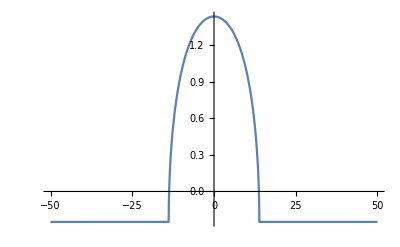

```mathematica
Plot[gTotal[μ,-3,4.45],{μ,-50,50}]
```

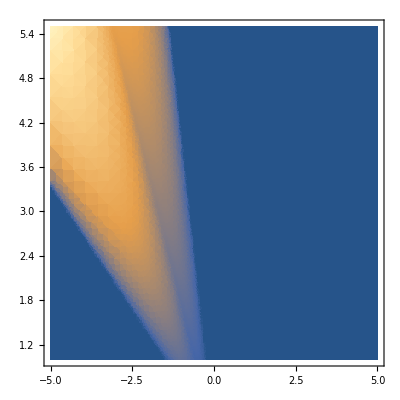

```mathematica
DensityPlot[gTotal[0,ωp,Pplot],{ωp,-5,5},{Pplot,1,5.5},ColorFunction->"SunsetColors", MaxRecursion->5]
```

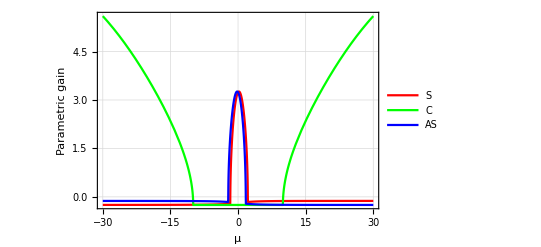

```mathematica
Plot[{gS[μ,-6.5,0,0,0]/.{Pp->13.8,κ->1},gC[μ,-6.5,0,0,0]/.{Pp->13.8,κ->1},gAS[μ,-6.5,0,0,0]/.{Pp->13.8,κ->1}},{μ,-30,30},PlotRange->{Full,Full},FrameLabel->{"μ","Parametric gain"},Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,{Blue},{Orange,Dashed}}, ScalingFunctions->{"Reverse",Identity},PlotLegends->{"S", "C", "AS"}]
```

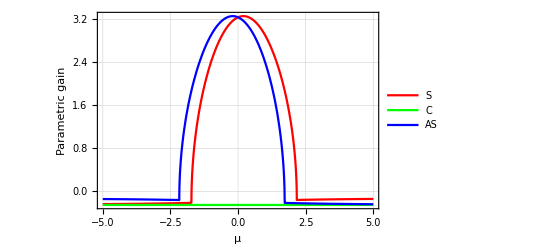

```mathematica
Plot[{gS[μ,-6.5,0,0,0]/.{Pp->13.8,κ->1},gC[μ,-6.5,0,0,0]/.{Pp->13.8,κ->1},gAS[μ,-6.5,0,0,0]/.{Pp->13.8,κ->1}},{μ,-5,5},PlotRange->{Full,Full},FrameLabel->{"μ","Parametric gain"},Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,{Blue},{Orange,Dashed}}, ScalingFunctions->{"Reverse",Identity},PlotLegends->{"S", "C", "AS"}]
```

### Export

```mathematica
muVals=Range[-30,30,0.1];
```

```mathematica
data=Table[{mu,gS[mu,-1.75,0,0,0]/. {Pp->3.45,κ->1},gC[mu,-1.75,0,0,0]/. {Pp->3.45,κ->1},gAS[mu,-1.75,0,0,0]/. {Pp->3.45,κ->1}},{mu,muVals}];
```

General::munfl: -4.03643×10^-308 0.056026 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -4.03643×10^-308 4.40355×10^-17 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -4.03643×10^-308 0.056026 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
dataWithHeader=Prepend[data,{"mu","gS","gC","gAS"}];
```

```mathematica
Export["G:\\.shortcut-targets-by-id\\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\\LPD Team\\uploads\\Luca\\Mathematica\\OPO in oOo\\oOo_assymetric_parametric_gain.csv",dataWithHeader]
```

G:\.shortcut-targets-by-id\0B-cdi4XK3uCzaTA4dHBYZkx5ZWs\LPD Team\uploads\Luca\Mathematica\OPO in oOo\oOo_assymetric_parametric_gain.csv

# 600 800

## Coupled mode theory

```mathematica
ClearAll["Global`*"]
```

```mathematica
H[μ_]:=({{(ω1[μ]-d1×μ), -J, 0}, {-J, (ω2[μ]-d1×μ), -J}, {0, -J, (ω3[μ]-d1×μ)}});
```

```mathematica
ω1[μ_]:=ω0 +d1×μ + d2/2 μ^2+δ1;
ω2[μ_]:=ω0 + D1×(2μ) + D2/2(2μ)^2+δ2;
ω3[μ_]:=ω0+d1×μ + d2/2 μ^2 +δ3;
```

```mathematica
δ1=-.2;δ2= -0.168;δ3= -.252;
δ1=0;δ2= 0;δ3= 0;
```

## Dispersion

```mathematica
d1=451.85; (* FSR *)
d2=-7.56×10^-3; (* GVD *)
D1=451.85*0.9944/2;
D2=-7.56×10^-3;
J=9.57627730727495/(√2);(* Splitting *)
ω0=0;
```

## Coupled modes in function of μ

```mathematica
sortedEig[μ_]:=sortedEig[μ]=Module[{vals,vecs,pairs,fixSign},(*flip sign if the first component is negative*)
fixSign[v_]:=v/Sign[v[[1]]];
(*If[Re[v[[1]]]<0,-v,v];*)
{vals,vecs}=Eigensystem[H[μ]];
vecs=fixSign/@vecs;
pairs=Transpose[{vals,vecs}];
SortBy[pairs,First]];
```

```mathematica
ωS[μ_]:=sortedEig[μ][[1,1]];  (*smallest eigenvalue*)
bS[μ_]:=Normalize[sortedEig[μ][[1,2]]];

ωC[μ_]:=sortedEig[μ][[2,1]];
bC[μ_]:=Normalize[sortedEig[μ][[2,2]]];

ωAS[μ_]:=sortedEig[μ][[3,1]];  (*largest eigenvalue*)
bAS[μ_]:=Normalize[sortedEig[μ][[3,2]]];
```

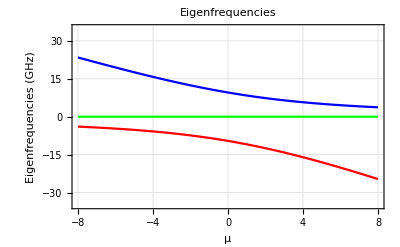

```mathematica
Plot[{ωS[μ]-ωC[μ],ωC[μ]-ωC[μ],ωAS[μ]-ωC[μ]},{μ,-8,8},FrameLabel->{"μ","Eigenfrequencies (GHz)"},PlotLabel->"Eigenfrequencies",PlotRange->{{-8,8},{-35,35}},Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue}]
```

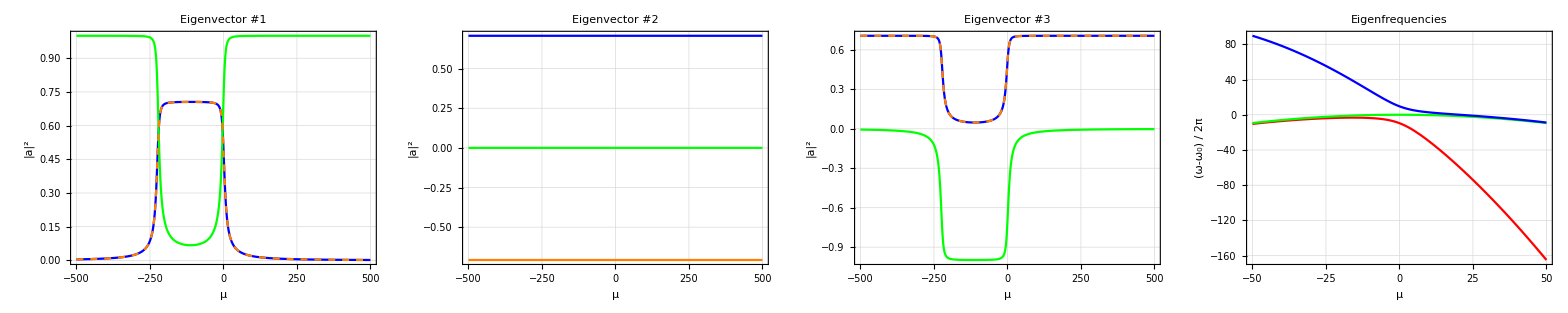

```mathematica
plt1=Plot[{bS[μ][[1]],bS[μ][[2]],bS[μ][[3]]},{μ,-500,500},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #1",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Blue,Green,{Orange,Dashed}}];
plt2=Plot[{bC[μ][[1]],bC[μ][[2]],bC[μ][[3]]},{μ,-500,500},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #2",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Blue,Green,Orange}];
plt3=Plot[{bAS[μ][[1]],bAS[μ][[2]],bAS[μ][[3]]},{μ,-500,500},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #3",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Blue,Green,{Orange,Dashed}}];
plt4=Plot[{ωS[μ],ωC[μ],ωAS[μ]},{μ,-50,50},FrameLabel->{"μ","(ω-ω_0) / 2π"},PlotLabel->"Eigenfrequencies",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue}];
Grid[{{plt1,plt2,plt3,plt4}},ItemSize->Automatic,BaseStyle->ImageSizeMultipliers->1]
```

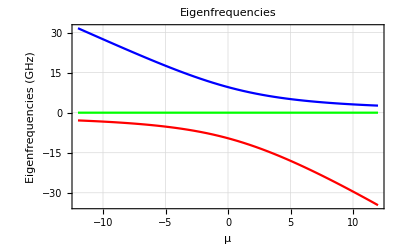

```mathematica
Plot[{ωS[μ]-ωC[μ],ωC[μ]-ωC[μ],ωAS[μ]-ωC[μ]},{μ,-12,12},FrameLabel->{"μ","Eigenfrequencies (GHz)"},PlotLabel->"Eigenfrequencies",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue}]
```

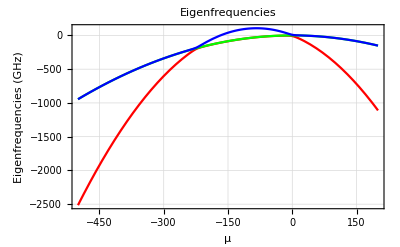

```mathematica
Plot[{ωS[μ],ωC[μ],ωAS[μ]},{μ,-500,200},FrameLabel->{"μ","Eigenfrequencies (GHz)"},PlotLabel->"Eigenfrequencies",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue}]
```

```mathematica
Print[bS[0]//MatrixForm, bC[0]//MatrixForm, bAS[0]//MatrixForm]
```

(0.5
0.707107
0.5)(0.707107
-9.27478×10^-16
-0.707107)(0.5
-0.707107
0.5)

```mathematica
Print[{ωS[0]-ωC[0], ωC[0]-ωC[0], ωAS[0]-ωC[0]}]
```

{-9.57628,0.,9.57628}

```mathematica
Print[bS[-1]//MatrixForm, bC[-1]//MatrixForm, bAS[-1]//MatrixForm]
```

(0.531602
0.659393
0.531602)(0.707107
-9.27478×10^-16
-0.707107)(0.466261
-0.751798
0.466261)

```mathematica
Print[{ωS[-1]-ωC[-1], ωC[-1]-ωC[-1], ωAS[-1]-ωC[-1]}]
```

{-8.39924,0.,10.9183}

## Overlapping

```mathematica
ΓS[μ_,δ1_,δ2_,δ3_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bS[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]]^2,{i,1,3}]
ΓC[μ_,δ1_,δ2_,δ3_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bC[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]]^2,{i,1,3}]
ΓAS[μ_,δ1_,δ2_,δ3_]:=Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bAS[μ][[i]]]*1/(1+KroneckerDelta[2,i])bC[0][[i]]]^2,{i,1,3}]
```

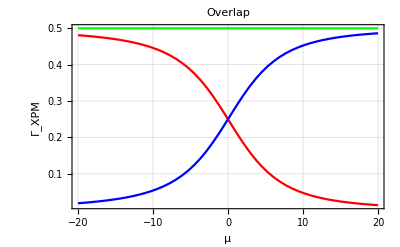

```mathematica
Plot[{ΓS[μ,0,0,0],ΓC[μ,0,0,0],ΓAS[μ,0,0,0]},{μ,-20,20},FrameLabel->{"μ","Γ_XPM"},PlotLabel->"Overlap",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[Black,14],PlotStyle->{Red,Green,Blue, {Orange,Dashed}}]
```

```mathematica
PSBS = Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bS[μp][[i]]]*1/(1+KroneckerDelta[2,i])bS[μb][[i]]]^2,{i,1,3}];
PSBC = Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bS[μp][[i]]]*1/(1+KroneckerDelta[2,i])bC[μb][[i]]]^2,{i,1,3}];
PSBAS = Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bS[μp][[i]]]*1/(1+KroneckerDelta[2,i])bAS[μb][[i]]]^2,{i,1,3}];
PCBS = Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bC[μp][[i]]]*1/(1+KroneckerDelta[2,i])bS[μb][[i]]]^2,{i,1,3}];
PCBC = Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bC[μp][[i]]]*1/(1+KroneckerDelta[2,i])bC[μb][[i]]]^2,{i,1,3}];
PCBAS = Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bC[μp][[i]]]*1/(1+KroneckerDelta[2,i])bAS[μb][[i]]]^2,{i,1,3}];
PASBS = Sum[Abs[1/(1+KroneckerDelta[2,i])Conjugate[bAS[μp][[i]]]*1/(1+KroneckerDelta[2,i])bS[μb][[i]]]^2,{i,1,3}];
PASBC = Sum[Abs[Conjugate[bAS[μp][[i]]]*bC[μb][[i]]]^2,{i,1,3}];
PASBAS = Sum[Abs[Conjugate[bAS[μp][[i]]]*bAS[μb][[i]]]^2,{i,1,3}];
```

```mathematica
(*PSBS = Sum[Abs[Conjugate[bS[μp][[i]]]*bS[μb][[i]]]^2,{i,1,3}];
PSBC = Sum[Abs[Conjugate[bS[μp][[i]]]*bC[μb][[i]]]^2,{i,1,3}];
PSBAS = Sum[Abs[Conjugate[bS[μp][[i]]]*bAS[μb][[i]]]^2,{i,1,3}];
PCBS = Sum[Abs[Conjugate[bC[μp][[i]]]*bS[μb][[i]]]^2,{i,1,3}];
PCBC = Sum[Abs[Conjugate[bC[μp][[i]]]*bC[μb][[i]]]^2,{i,1,3}];
PCBAS = Sum[Abs[Conjugate[bC[μp][[i]]]*bAS[μb][[i]]]^2,{i,1,3}];
PASBS = Sum[Abs[Conjugate[bAS[μp][[i]]]*bS[μb][[i]]]^2,{i,1,3}];
PASBC = Sum[Abs[Conjugate[bAS[μp][[i]]]*bC[μb][[i]]]^2,{i,1,3}];
PASBAS = Sum[Abs[Conjugate[bAS[μp][[i]]]*bAS[μb][[i]]]^2,{i,1,3}];*)
```

```mathematica
({{PSBS, PSBC, PSBAS}, {PCBS, PCBC, PCBAS}, {PASBS, PASBC, PASBAS}})/.{μp->-1,μb->0}//MatrixForm
```

(0.154888 | 0.2826 | 0.154888
0.25 | 0.5 | 0.25
0.126362 | 0.2174 | 0.3913)

```mathematica
({{PSBS/PSBS, PSBC/PSBS, PSBAS/PSBS}, {PCBS/PCBC, PCBC/PCBC, PCBAS/PCBC}, {PASBS/PASBAS, PASBC/PASBAS, PASBAS/PASBAS}})/.{μp->-1,μb->0}//MatrixForm
```

(1 | 1.82455 | 1.
0.5 | 1 | 0.5
0.32293 | 0.555583 | 1)

```mathematica
offset=-.5;
({{PSBS/PSBS, PSBC/PSBS, PSBAS/PSBS}, {PCBS/PCBC, PCBC/PCBC, PCBAS/PCBC}, {PASBS/PASBAS, PASBC/PASBAS, PASBAS/PASBAS}})/.{μp->-1+offset,μb->0+offset}//MatrixForm
```

(1 | 0.858617 | 1.01991
0.532884 | 1 | 0.467116
0.936989 | 0.489452 | 1)